```mathematica
(*Quit[]*)
```

# Form Factors

## Init

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
<<"funcs.m"
```

```mathematica
<<"./mdat/amps.mdat";
```

## Ebert

```mathematica
json = Import["../literatute/Ebert_1007.1369/Fig3.json"];
```

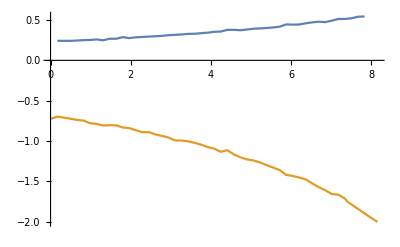

```mathematica
fact=0.8679;
tab$fMinus = extractFF[json,1,-fact]["data"];
tab$fPlus = extractFF[json, 2, fact]["data"];
ListPlot[{tab$fPlus, tab$fMinus}, Joined->True]
```

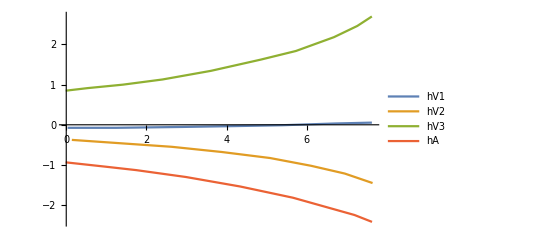

```mathematica
fact=0.8679;
tab$hV1 = extractFF[json,3, fact]["data"];
tab$hV2 = extractFF[json,4, -fact]["data"];
tab$hV3 = extractFF[json,5,fact]["data"];
tab$hA = extractFF[json,6,-fact]["data"];
ListPlot[{tab$hV1,tab$hV2,tab$hV3, tab$hA}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

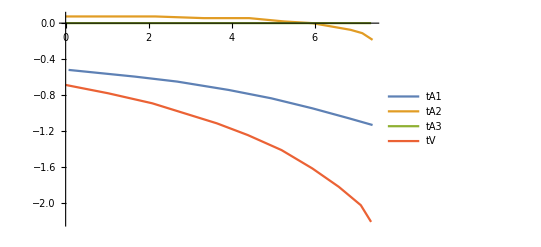

```mathematica
fact = 0.8679;
tab$tA3 = extractFF[json, 7, fact]["data"];
tab$tA2 = extractFF[json, 8, fact]["data"];
tab$tA1 = extractFF[json, 9, -fact]["data"];
tab$tV = extractFF[json, 10,-fact]["data"];
ListPlot[{tab$tA1, tab$tA2, tab$tA3, tab$tV},Joined->True, PlotLegends->{"tA1", "tA2", "tA3", "tV"}, PlotRange->All]
```

```mathematica
ffFitRule = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]], fitFunc,fitParams,q2]]
,{ff, ffList}];
```

```mathematica
str="";
Do[
str=str<>"*"<>ToString[f⟦1,0⟧]<>"="<>ToString[CForm[f⟦2⟧/.Power->pow]]<>";\n"
,{f, ffFitRule}];
str
```

*fPlus=0.23282300350057755 + 0.019996139209756715*q2 + 0.001768814758168807*pow(q2,2) + 0.00009802467740735175*pow(q2,3);
*fMinus=-0.6900138885624459 - 0.08025272843176387*q2 + 0.0009309233248790164*pow(q2,2) - 0.0012853786490662072*pow(q2,3);
*hV1=-0.07554456322305214 - 0.0019950279470936543*q2 + 0.0033385897592174115*pow(q2,2) - 0.00010895447116604855*pow(q2,3);
*hV2=-0.36177101202457995 - 0.087653808464362*q2 + 0.011963515946408414*pow(q2,2) - 0.00248097238192017*pow(q2,3);
*hV3=0.8405530963460115 + 0.13289457943506788*q2 - 0.012189973937580784*pow(q2,2) + 0.0034226277865052135*pow(q2,3);
*hA=-0.9323204885565738 - 0.1077393424732536*q2 - 0.0007600453975902571*pow(q2,2) - 0.001362065788893639*pow(q2,3);
*tV=-0.6767943173708638 - 0.1229162643796341*q2 + 0.014440210489932203*pow(q2,2) - 0.003435853193714721*pow(q2,3);
*tA1=-0.5176668452675808 - 0.035281507568182296*q2 - 0.004625298576965595*pow(q2,2) - 0.00025444206488251994*pow(q2,3);
*tA2=0.08102831028164982 - 0.028756326363329292*q2 + 0.01391101310098692*pow(q2,2) - 0.0019521666768316586*pow(q2,3);
*tA3=0.;

```mathematica
DeleteFile["./mdat/ebert_ff.mdat"];
file = OpenWrite["./mdat/ebert_ff.mdat"];
WriteString[file, ToString[Definition[ffFitRule], InputForm]<>"\n"];
WriteString[file, ToString[Definition[ffFitRule$2P], InputForm]<>"\n"];
Close[file];
```

## Wang et al, arXiv:1107:0474 [hep-ph]

```mathematica
json = Import["../literatute/1107.0474/fig3_FF.json"];
```

```mathematica
(* we have distribution over q2max - q2 on the plot! *)
Clear[getMcc];
GeV=1.; MeV=10^-3 GeV;
$MBc = 6274.47MeV;
(* 1P masses from PDG *)
getMcc[out_, type_:"1P"]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
(* 2P masses are chosen to fit Ebert's distributions *)
getMcc[out_, "2P"]:=Switch[out,"chi_c0", 3862MeV,"chi_c1", 3.9214,"chi_c2",3.967735]
q2Max[out_]:=($MBc-getMcc[out])^2;
```

```mathematica
Clear[reflect];
reflect[tab_,out_]:=Module[{newTab=tab},
newTab⟦All,1⟧=q2Max[out]-newTab⟦All,1⟧;
newTab
];
```

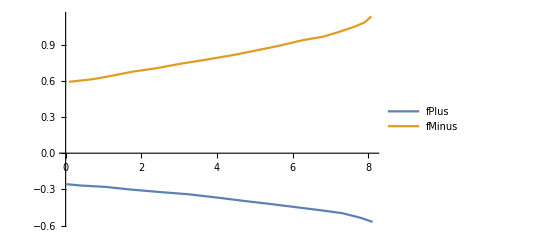

```mathematica
out="chi_c0";
fact = 0.748;
tab$fPlus = extractFF[json, 1, -fact]⟦"data"⟧//reflect[#,out]&;
tab$fMinus= extractFF[json,2, fact]⟦"data"⟧//reflect[#,out]&;
ListPlot[{tab$fPlus,tab$fMinus}, Joined->True, PlotLegends->{"fPlus","fMinus"}]
```

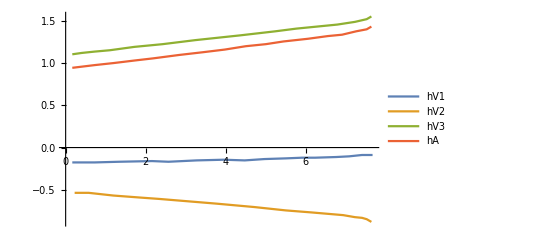

```mathematica
out="chi_c1";
fact = 0.732;
tab$hV1 = extractFF[json, 3, -fact]⟦"data"⟧//reflect[#,out]&;
tab$hV2 = extractFF[json, 4, -fact]⟦"data"⟧//reflect[#,out]&;
tab$hV3 = extractFF[json, 5 , fact]⟦"data"⟧//reflect[#,out]&;
tab$hA = extractFF[json, 6 ,fact]⟦"data"⟧//reflect[#,out]&;
ListPlot[{tab$hV1,tab$hV2,tab$hV3, tab$hA}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

```mathematica
extractNames[json]
```

(1 | chi0: -sPlus
2 | chi0_sMinus
3 | chi1: -f
4 | chi1: -u1
5 | chi1:u2
6 | chi1:g
7 | chi2:-c1
8 | chi2:-k
9 | chi2:c2
10 | chi2:h)

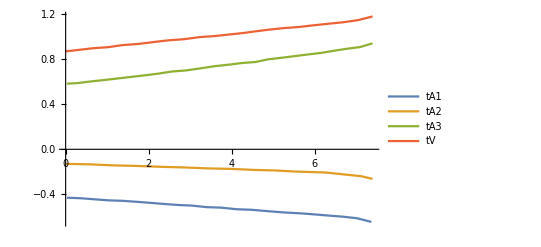

```mathematica
out="chi_c2";
fact = 0.430;
tab$tA2 = extractFF[json, 7, -fact]⟦"data"⟧//reflect[#,out]&;
tab$tA1 = extractFF[json, 8, -fact]⟦"data"⟧//reflect[#,out]&;
tab$tA3 = extractFF[json, 9, fact]⟦"data"⟧//reflect[#,out]&;
tab$tV = extractFF[json, 10,fact]⟦"data"⟧//reflect[#,out]&;
ListPlot[{tab$tA1, tab$tA2, tab$tA3, tab$tV},Joined->True, PlotLegends->{"tA1", "tA2", "tA3", "tV"}, PlotRange->All]
```

```mathematica
fitFunc=a0+a1 q2 + a2 q2^2+a3 q2^3;
fitParams = DeleteCases[Variables[fitFunc] ,q2]
```

{a0,a1,a2,a3}

```mathematica
ffFitRule$Wang = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]], fitFunc,fitParams,q2]]
,{ff, ffList}]
```

{fPlus(q2_):>-0.000348281 q2^3+0.0018872 q2^2-0.0299383 q2-0.254256,fMinus(q2_):>0.000814326 q2^3-0.00657645 q2^2+0.0659497 q2+0.576102,hV1(q2_):>0.000162205 q2^3-0.000668611 q2^2+0.00756277 q2-0.178867,hV2(q2_):>-0.000414285 q2^3+0.00312312 q2^2-0.0441231 q2-0.520004,hV3(q2_):>0.000520855 q2^3-0.00502003 q2^2+0.0658704 q2+1.09319,hA(q2_):>0.000450084 q2^3-0.00376052 q2^2+0.0659085 q2+0.931121,tV(q2_):>0.000254525 q2^3-0.00225139 q2^2+0.0436616 q2+0.868286,tA1(q2_):>-0.000295842 q2^3+0.00233561 q2^2-0.0294099 q2-0.425225,tA2(q2_):>-0.000524051 q2^3+0.00426751 q2^2-0.0204552 q2-0.125631,tA3(q2_):>0.000146115 q2^3-0.000466823 q2^2+0.0434767 q2+0.577121}

```mathematica
DeleteFile["./mdat/wang_ff.mdat"];
file = OpenWrite["./mdat/wang_ff.mdat"];
WriteString[file, ToString[Definition[ffFitRule$Wang], InputForm]<>"\n"];
Close[file];
```

```mathematica
str="// Wnang's FF\n\n";
Do[
str=str<>"*"<>ToString[f⟦1,0⟧]<>"="<>ToString[CForm[f⟦2⟧/.Power->pow]]<>";\n"
,{f, ffFitRule$Wang}]
str
```

// Wnang's FF

*fPlus=-0.25425552682836877 - 0.029938283037836827*q2 + 0.0018872048185675327*pow(q2,2) - 0.00034828076552277453*pow(q2,3);
*fMinus=0.5761019473812443 + 0.0659496955579663*q2 - 0.006576446752598759*pow(q2,2) + 0.0008143261736504712*pow(q2,3);
*hV1=-0.17886747969811198 + 0.0075627665394510215*q2 - 0.0006686110968932466*pow(q2,2) + 0.00016220546540721533*pow(q2,3);
*hV2=-0.5200037833399105 - 0.04412311688421822*q2 + 0.0031231169479816663*pow(q2,2) - 0.00041428486069832273*pow(q2,3);
*hV3=1.0931870462254507 + 0.06587035754776979*q2 - 0.0050200293358184786*pow(q2,2) + 0.0005208548635047951*pow(q2,3);
*hA=0.931120941094141 + 0.06590852925652363*q2 - 0.0037605169566740444*pow(q2,2) + 0.0004500841991378414*pow(q2,3);
*tV=0.868286364938619 + 0.0436616014696729*q2 - 0.0022513905200994334*pow(q2,2) + 0.0002545250114905908*pow(q2,3);
*tA1=-0.4252247922646758 - 0.02940985772910558*q2 + 0.002335614376282232*pow(q2,2) - 0.00029584210990627466*pow(q2,3);
*tA2=-0.12563088829655486 - 0.020455237690167768*q2 + 0.004267512415301323*pow(q2,2) - 0.0005240508709010183*pow(q2,3);
*tA3=0.577120784738489 + 0.04347672426601775*q2 - 0.00046682260784860704*pow(q2,2) + 0.00014611522821803905*pow(q2,3);

## Henandez, hep-ph/0607150v3

```mathematica
json = Import["..//literatute/Hernandez_0607150/chi_c0.json"];
```

```mathematica
extractNames[json]
```

(1 | -fMinus
2 | fPlus)

```mathematica
<<"./mdat/amps.mdat";
```

```mathematica
P = p1+p2; q=p1-p2;
```

```mathematica
ScalarProduct[p2, eps]=0;
```

```mathematica
amplitude["chi_c1","V"]
```

hV1(q2) (MBc+Mcc) (ḡ)^amu+((OverBar[p1]-OverBar[p2])^a (hV2(q2) OverBar[p1]^mu+hV3(q2) OverBar[p2]^mu))/MBc

```mathematica
Pair[Momentum[p2],LorentzIndex[a]]=0;Pair[Momentum[p2],LorentzIndex[b]]=0;
```

```mathematica
out = "chi_c0";
ampH[out]=Calc[FV[P,mu]FPlus + FV[q,mu]Fminus]
```

Fminus OverBar[p1]^mu-Fminus OverBar[p2]^mu+FPlus OverBar[p1]^mu+FPlus OverBar[p2]^mu

```mathematica
diff = (ampH[out]-amplitude[out, "V+A"])//Calc//Collect[#, Pair[__]]&//ReplaceAll[#, a_[q2]:>a]&
Solve[#==0&/@(Select[#, FreeQ[#, Pair[__]]&]&/@List@@diff), {fPlus, fMinus}]
```

OverBar[p1]^mu (-fMinus+Fminus-fPlus+FPlus)+OverBar[p2]^mu (fMinus-Fminus-fPlus+FPlus)

{{fPlus→FPlus,fMinus→Fminus}}

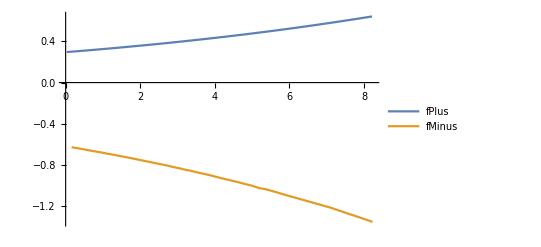

```mathematica
out="chi_c0";
tab$fMinus= extractFF[json, 1, -1]⟦"data"⟧;
tab$fPlus = extractFF[json, 2]⟦"data"⟧;
ListPlot[{tab$fPlus,tab$fMinus}, Joined->True, PlotLegends->{"fPlus","fMinus"}]
```

```mathematica
ffFitRule$Hernandez  = {};
```

```mathematica
AppendTo[ffFitRule$Hernandez, fPlus[q2_]:>Evaluate[fitFunc/.FindFit[extractFF[json, 2]["data"], fitFunc, fitParams,q2]]];
AppendTo[ffFitRule$Hernandez, fMinus[q2_]:>Evaluate[fitFunc/.FindFit[extractFF[json, 1,-1]["data"], fitFunc, fitParams,q2]]];
```

```mathematica
out = "chi_c1"
```

chi_c1

```mathematica
Clear[MBc, Mcc, V, A0, Aplus, Aminus];
```

```mathematica
ampH[out]=I(-1/(MBc+Mcc)LeviCivita[mu, a][P,q]V-I((MBc-Mcc)MT[a,mu]A0-FV[P,a]/(MBc+Mcc)(FV[P,mu]Aplus+FV[q,mu]Aminus)))
```

ⅈ (-(V (ϵ̄)^(muaOverBar[p1]+OverBar[p2]OverBar[p1]-OverBar[p2]))/(MBc+Mcc)-ⅈ (A0 (MBc-Mcc) (ḡ)^amu-((OverBar[p1]+OverBar[p2])^a (Aminus (OverBar[p1]-OverBar[p2])^mu+Aplus (OverBar[p1]+OverBar[p2])^mu))/(MBc+Mcc)))

```mathematica
amplitude[out, "V+A"]
```

hV1(q2) (MBc+Mcc) (ḡ)^amu+(2 ⅈ hA(q2) (ϵ̄)^(mua OverBar[p1]OverBar[p2]))/(MBc+Mcc)+((OverBar[p1]-OverBar[p2])^a (hV2(q2) OverBar[p1]^mu+hV3(q2) OverBar[p2]^mu))/MBc

```mathematica
diff = (ampH[out]-amplitude[out, "V+A"])//Calc//Collect2[#, Pair[__]]&//ReplaceAll[#, a_[q2]:>a]&;
sol = Solve[#==0&/@(Select[#, FreeQ[#, Pair[__]]&]&/@List@@diff), {hV1, hV2, hV3, hA}]//Simplify
```

{{hV1→(A0 (MBc-Mcc))/(MBc+Mcc),hV2→-(MBc (Aminus+Aplus))/(MBc+Mcc),hV3→(MBc (Aminus-Aplus))/(MBc+Mcc),hA→V}}

```mathematica
json = Import["..//literatute/Hernandez_0607150/chi_c1.json"];
extractNames[json]
```

(1 | V
2 | -Aminus
3 | Aplus
4 | -A0)

```mathematica
GeV=1.; MeV=10^-3 GeV;
$MBc = 6274.47MeV;
getMcc[out_, type_:"1P"]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
Mcc = getMcc[out];
```

```mathematica
V =fitFunc/.FindFit[extractFF[json, 1]["data"], fitFunc, fitParams,q2];
Aminus = fitFunc/.FindFit[extractFF[json, 2,-1]["data"], fitFunc, fitParams,q2];
Aplus = fitFunc/.FindFit[extractFF[json, 3]["data"], fitFunc, fitParams,q2];
A0 = fitFunc/.FindFit[extractFF[json, 4,-1]["data"], fitFunc, fitParams,q2];
```

```mathematica
MBc = $MBc; Mcc = getMcc[out];
```

```mathematica
AppendTo[ffFitRule$Hernandez, hV1[q2_]:>Evaluate[hV1/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, hV2[q2_]:>Evaluate[hV2/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, hV3[q2_]:>Evaluate[hV3/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, hA[q2_]:>Evaluate[hA/.sol⟦1⟧]];
```

```mathematica
Clear[MBc, Mcc, V, Aminus, Aplus, A0];
```

```mathematica
ffFitRule$Hernandez
```

{fPlus(q2_):>0.0000383431 q2^3+0.00132974 q2^2+0.0285995 q2+0.29509,fMinus(q2_):>-0.0000875188 q2^3-0.00260265 q2^2-0.0616112 q2-0.616289,hV1(q2_):>0.282449 (0.000132981 q2^3+0.00274719 q2^2-0.00587502 q2-0.499608),hV2(q2_):>-0.641224 (-0.0000452249 q2^3-0.00377286 q2^2-0.0553996 q2-0.5194),hV3(q2_):>0.641224 (0.000158543 q2^3-0.00829041 q2^2-0.116802 q2-1.41045),hA(q2_):>0.0000804839 q2^3+0.00393839 q2^2+0.0864898 q2+0.91581}

### chi_c2

```mathematica
out = "chi_c2";
```

```mathematica
ampH[out]=I(LeviCivita[mu, a][P,q]FV[P,b]T4-I(MT[mu, b]*FV[P,a]T1+FV[P,a]FV[P,b](FV[P,mu]T2+FV[q,mu]T3)))
```

ⅈ (T4 (OverBar[p1]+OverBar[p2])^b (ϵ̄)^(muaOverBar[p1]+OverBar[p2]OverBar[p1]-OverBar[p2])-ⅈ (T1 (OverBar[p1]+OverBar[p2])^a (ḡ)^bmu+(OverBar[p1]+OverBar[p2])^a (OverBar[p1]+OverBar[p2])^b (T2 (OverBar[p1]+OverBar[p2])^mu+T3 (OverBar[p1]-OverBar[p2])^mu)))

```mathematica
diff = (ampH[out]-amplitude[out, "V+A"])//Calc//Collect2[#, Pair[__]]&//ReplaceAll[#, a_[q2]:>a]&;
```

```mathematica
diff
```

(OverBar[p1]^a (ḡ)^bmu (MBc T1-MBc tA1-Mcc tA1))/MBc+(2 ⅈ OverBar[p1]^b (MBc^2 T4+MBc Mcc T4+tV) (ϵ̄)^(amu OverBar[p1]OverBar[p2]))/(MBc (MBc+Mcc))+(OverBar[p1]^a OverBar[p1]^b OverBar[p2]^mu (MBc^2 T2-MBc^2 T3-tA3))/MBc^2+(OverBar[p1]^a OverBar[p1]^b OverBar[p1]^mu (MBc^2 T2+MBc^2 T3-tA2))/MBc^2

```mathematica
sol = Solve[#==0&/@(Select[#, FreeQ[#, Pair[__]]&]&/@List@@diff), {tA1, tA2, tA3, tV}]//Simplify
```

{{tA1→(MBc T1)/(MBc+Mcc),tA2→MBc^2 (T2+T3),tA3→MBc^2 (T2-T3),tV→-MBc T4 (MBc+Mcc)}}

```mathematica
json = Import["..//literatute/Hernandez_0607150/chi_c2.json"];
extractNames[json]
```

(1 | T1
2 | T2
3 | T3
4 | T4)

```mathematica
T1 =fitFunc/.FindFit[extractFF[json, 1]["data"], fitFunc, fitParams,q2];
T2 = fitFunc/.FindFit[extractFF[json, 2]["data"], fitFunc, fitParams,q2];
T3 = fitFunc/.FindFit[extractFF[json, 3]["data"], fitFunc, fitParams,q2];
T4 = fitFunc/.FindFit[extractFF[json, 4]["data"], fitFunc, fitParams,q2];
```

```mathematica
MBc = $MBc; Mcc = getMcc[out];
```

```mathematica
sol
```

{{tA1→0.638257 (-0.000379051 q2^3+0.0100917 q2^2+0.0703184 q2+1.0255),tA2→39.369 (-0.000142326 q2^3+0.00178439 q2^2-0.00434717 q2+0.197284),tA3→39.369 (-0.000067087 q2^3+0.000406928 q2^2-0.00324985 q2-0.0237744),tV→-61.6821 (5.18204×10^-6 q2^3+0.000373763 q2^2-0.000335872 q2+0.109458)}}

```mathematica
AppendTo[ffFitRule$Hernandez,tA1[q2_]:>Evaluate[tA1/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, tA2[q2_]:>Evaluate[tA2/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, tA3[q2_]:>Evaluate[tA3/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, tV[q2_]:>Evaluate[tV/.sol⟦1⟧]];
```

```mathematica
ffFitRule$Hernandez
```

{fPlus(q2_):>0.0000383431 q2^3+0.00132974 q2^2+0.0285995 q2+0.29509,fMinus(q2_):>-0.0000875188 q2^3-0.00260265 q2^2-0.0616112 q2-0.616289,hV1(q2_):>0.282449 (0.000132981 q2^3+0.00274719 q2^2-0.00587502 q2-0.499608),hV2(q2_):>-0.641224 (-0.0000452249 q2^3-0.00377286 q2^2-0.0553996 q2-0.5194),hV3(q2_):>0.641224 (0.000158543 q2^3-0.00829041 q2^2-0.116802 q2-1.41045),hA(q2_):>0.0000804839 q2^3+0.00393839 q2^2+0.0864898 q2+0.91581,tA1(q2_):>0.638257 (-0.000379051 q2^3+0.0100917 q2^2+0.0703184 q2+1.0255),tA2(q2_):>39.369 (-0.000142326 q2^3+0.00178439 q2^2-0.00434717 q2+0.197284),tA3(q2_):>39.369 (-0.000067087 q2^3+0.000406928 q2^2-0.00324985 q2-0.0237744),tV(q2_):>-61.6821 (5.18204×10^-6 q2^3+0.000373763 q2^2-0.000335872 q2+0.109458)}

```mathematica
DeleteFile["./mdat/hernandez_ff.mdat"];
file = OpenWrite["./mdat/hernandez_ff.mdat"];
WriteString[file, ToString[Definition[ffFitRule$Hernandez], InputForm]<>"\n"];
Close[file];
```